# Quantum Operations: How to Describe Quantum Decoherence Process

Let the “system” be initially in quantum state ρ.

In the presence of coupling between the “system” and “environment”, the density operator evolves from ρ to ρ'

Question: What is the general relation between ρ and ρ'.

## Unitary Dynamics

### Pure State

Starting from ψ at t=0, the state vector evolves to ψ' at time τ; ψ→ψ'. The evolution is governed by the Schrödinger equation

ⅈ d/dt ψ=Hψ .

The relation between the initial and final states is summarized by a unitary operator.

ψ'=Uψ

### Mixed State

Starting from ρ at t=0, the state vector evolves to ρ' at time τ; ρ→ρ'. The evolution is governed by the Schrödinger equation

ⅈ d/dt ρ=-ⅈ [H,ρ] .

The relation between the initial and final states is summarized by a unitary operator.

ρ'=Uρ U^†

## Quantum Dissipative Dynamics

### Summary

The relation between the initial and final states is summarized by a completely positive supermap ℱ:ρ↦ρ'.

In the Kraus representation, ℱ can be rewritten in the form

ρ'=ℱ[ρ]=Σ_μ F_μ ρ F_μ^† ,

where F_μ:𝒱→𝒱 is a linear operator on the Hilbert space 𝒱 of the system in question.

One can optimize the Kraus representation by properly choosing maximum d^2 Kraus elements F_μ so that

ℱ[ρ]=Σ_(μ=0)^(d^2-1)F_μ ρ F_μ^† ,

### System+Environment Model

Question: Physically, how does the Kraus representation arise?

Assume that the total system consisting of the system and environment is initially in the product state ρ⊗σ.

The total system is a closed system, hence,

ρ⊗ σ↦U(ρ⊗ σ)U^†.

Without access to the environment, one has to take a partial trace of the final state over the environment to obtain the state of the system.

ℱ(ρ)=Tr_ℰ[U(ρ⊗ σ)U^†]=Σ_i ε_iU (ρ⊗ σ)U^†ε_i,

where {ε_i|i=1,2,…,d_ℰ} is an orthonormal basis of ℰ of dimension d_ℰ.

To construct the Kraus elements, we first take the spectral decomposition of σ

σ=Σ_(j=1)^r s_js_j,

where r is the rank of σ, and the eigenvectors s_j of σ̂ have been normalized by their own eigenvalues s_j=s_js_j.

We then define linear maps (F̂)_ij:𝒱↦𝒲 for each i and j by

F_ij:=Tr_ℰ[(I⊗ε_is_j)^†U]=ε_iUs_j

to get

ℱ(ρ)=Σ_ij F_ij ρ F_ij^† .

We finally regard μ:=(i,j) as a collective index and identify (F̂)_μ≡(F̂)_ij to be the desired Kraus elements:

ℱ(ρ)=Σ_μ F_μ ρ F_μ^† .

Clearly, they satisfy the closure relation

Σ_μ F_μ^†F_μ=I.

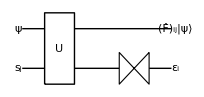

Figure 1. Quantum circuit describing the Kraus element (F̂)_ij corresponding to the dynamics of the system on condition that the environment has made a transition from the initial state s_j to state ε_i under the unitary interaction Û between the system and environment.

```mathematica
Let[Qubit,S]
```

Let us consider a chain of three qubits. The first qubit is regarded as the “system”, and the other two form the “environment”.

```mathematica
$L=3;
jj=Range[$L];
sys=1;
env=Range[2,$L];
```

Here is the Hamiltonian describing the chain. We are measuring the energy in units of B (B=1).

```mathematica
Let[Real,J]
H=S[sys,3]/2+J/2* Total[ChainBy[S[jj,1],Multiply]]
```

The system has a discrete symmetry. It is invariant under the rotation around the z-axis by angle π.

```mathematica
V=Rotation[Pi,S[1,3]]**Rotation[Pi,S[2,3]]**Rotation[Pi,S[3,3]]
V**H**Dagger[V]//Elaborate
```

The symmetry leads to the degeneracy of the eigenvalues of the Hamiltonian.

```mathematica
ProperValues[H]
```

The time-evolution operator of the chain is evaluated.

```mathematica
Let[Real,t]
U[t_]=Elaborate@MultiplyExp[-I t H];
```

We suppose that the chain is initially in the state L⊗L⊗L, where L=(0+i1)/√2.

```mathematica
Clear[vec]
vec[0]=ProductState[S@jj->{1,I}/Sqrt[2]]
vec[t_]=U[t]**Elaborate[vec[0]];
```

Here is a set of replacement rules to be used later to simplify expressions.

```mathematica
rules={Sqrt[1+J^2]->Ω,1/Sqrt[1+J^2]->1/Ω}
```

```mathematica
Clear[rho]
rho[t_]=PartialTrace[vec[t],S@env]//Elaborate//ExpToTrig//Garner;
rho[t]/.rules
```

Take a look at the dynamical evolution of the state of the “system” (the first qubit), after tracing out the “environment” (the other two qubits). On the left, shown is the evolution in the absence of the coupling to the environment. On the right, the evolution is not coherent due to the coupling to the environment. The evolution is still periodic because the environment is finite.

```mathematica
bv0=Block[{J=0.},Table[BlochVector[rho[2Pi*t]],{t,0,5,0.2}]];
bv=Block[{J=.5},Table[BlochVector[rho[2Pi*t]],{t,0,5/J,0.2}]];
GraphicsRow@{BlochSphere[{Blue,Bead/@bv0}],BlochSphere[{Red,Bead/@bv}]}
```

Now, let us examine the evolution in terms of the supermap. This is the initial state of the system.

```mathematica
in=Elaborate@ProductState[S[sys]->{1,I}/Sqrt[2]];
in=Elaborate@Dyad[in,in,S[sys]]
```

To find the Kraus elements, consider the initial state of the environment.

```mathematica
sgm=Elaborate@ProductState[S@env->{1,I}/Sqrt[2]]
```

Finally, this is the Kraus elements of the quantum operation.

```mathematica
bs=Basis[S@env];
prj=Map[Dyad[sgm,#,S@env]&,bs];
ops=U[t]**prj//Elaborate;
```

```mathematica
kraus=PartialTrace[#,S@env]&/@ops//ExpToTrig//Elaborate//Garner;
kraus/.rules
```

The Kraus elements above completely specifies the quantum operation.

```mathematica
spr=Supermap[kraus]
```

```mathematica
Clear[new]
new[t_]=spr[in]//Elaborate;
new[t]/.rules
```

```mathematica
new[t]-rho[t]//Elaborate//Garner
```

## Example: Communication without shared reference frame

S. D. Bartlett et al., Physical Review Letters 91, 027901 (2003), “Classical and Quantum Communication without a Shared Reference Frame.”

## Quantum Master Equation

In many cases, the time-evolution of density operator is governed by a quantum master equation of the form

ⅈ d/dt ρ=-ⅈ [H,ρ]+𝒟[ρ] .

We will discuss quantum master equation in a separate document.

## Summary

### Keywords

Quantum operations

Quantum noise

Quantum decoherence

### Functions

Supermap

PartialTrace

### Related Links

Section 5.2 of the Quantum Workbook (2022, 2023).

Tutorial: Quantum Operations